```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/ABISS/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L/input/kinematics.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L/input/equivalence_classes.m

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[1]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 344 counterterms of order 1

> 26 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 15 Particles insertions

Restoring 24 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

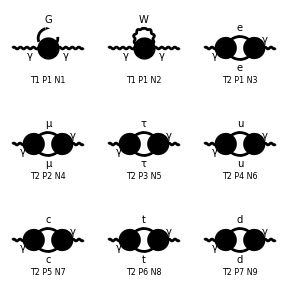

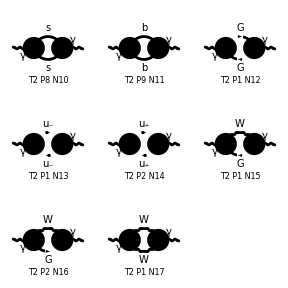

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

-(SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]

```mathematica
t[Lor1_,Lor2_]=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

((SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]-SP[{Lor1},{Lor2}])/(-1+d)

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[1],p_,i_]->1,Conjugate[PolarizationVector][V[1],p_,i_]->1}
```

{ep[V[1],p_,i_]→1,ep^*[V[1],p_,i_]→1}

## Interference

```mathematica
myAmp1LnoEP=myAmp1L/.removePolarizationVectors
```

{ⅈ EL^2 gFFAA (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2)] g[Lor1,Lor2],-(2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2)] g[Lor3,Lor4] (-ⅈ EL^2 gWWAA g[Lor1,Lor4] g[Lor2,Lor3]-ⅈ EL^2 gWWAA g[Lor1,Lor3] g[Lor2,Lor4]+2 ⅈ EL^2 gWWAA g[Lor1,Lor2] g[Lor3,Lor4]),-ⅈ (2 π)^-d FeynAmpDenominator[1/(-ME^2+(q1)^2),1/(-ME^2+(q1-k1)^2)] tr[ME+gs[-(q1)],ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+,ME+gs[-(q1)+k1],ⅈ EL gAl ga[Lor1].om_-+ⅈ EL gAl ga[Lor1].om_+],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MM^2+(q1)^2),1/(-MM^2+(q1-k1)^2)] tr[MM+gs[-(q1)],ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+,MM+gs[-(q1)+k1],ⅈ EL gAl ga[Lor1].om_-+ⅈ EL gAl ga[Lor1].om_+],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-ML^2+(q1)^2),1/(-ML^2+(q1-k1)^2)] tr[ML+gs[-(q1)],ⅈ EL gAl ga[Lor2].om_-+ⅈ EL gAl ga[Lor2].om_+,ML+gs[-(q1)+k1],ⅈ EL gAl ga[Lor1].om_-+ⅈ EL gAl ga[Lor1].om_+],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MU^2+(q1)^2),1/(-MU^2+(q1-k1)^2)] tr[MU+gs[-(q1)],ⅈ EL gAu ga[Lor2].om_-+ⅈ EL gAu ga[Lor2].om_+,MU+gs[-(q1)+k1],ⅈ EL gAu ga[Lor1].om_-+ⅈ EL gAu ga[Lor1].om_+] SumOver[Col3,3],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MC^2+(q1)^2),1/(-MC^2+(q1-k1)^2)] tr[MC+gs[-(q1)],ⅈ EL gAu ga[Lor2].om_-+ⅈ EL gAu ga[Lor2].om_+,MC+gs[-(q1)+k1],ⅈ EL gAu ga[Lor1].om_-+ⅈ EL gAu ga[Lor1].om_+] SumOver[Col3,3],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MT^2+(q1)^2),1/(-MT^2+(q1-k1)^2)] tr[MT+gs[-(q1)],ⅈ EL gAu ga[Lor2].om_-+ⅈ EL gAu ga[Lor2].om_+,MT+gs[-(q1)+k1],ⅈ EL gAu ga[Lor1].om_-+ⅈ EL gAu ga[Lor1].om_+] SumOver[Col3,3],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MD^2+(q1)^2),1/(-MD^2+(q1-k1)^2)] tr[MD+gs[-(q1)],ⅈ EL gAd ga[Lor2].om_-+ⅈ EL gAd ga[Lor2].om_+,MD+gs[-(q1)+k1],ⅈ EL gAd ga[Lor1].om_-+ⅈ EL gAd ga[Lor1].om_+] SumOver[Col3,3],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MS^2+(q1)^2),1/(-MS^2+(q1-k1)^2)] tr[MS+gs[-(q1)],ⅈ EL gAd ga[Lor2].om_-+ⅈ EL gAd ga[Lor2].om_+,MS+gs[-(q1)+k1],ⅈ EL gAd ga[Lor1].om_-+ⅈ EL gAd ga[Lor1].om_+] SumOver[Col3,3],-ⅈ (2 π)^-d FeynAmpDenominator[1/(-MB^2+(q1)^2),1/(-MB^2+(q1-k1)^2)] tr[MB+gs[-(q1)],ⅈ EL gAd ga[Lor2].om_-+ⅈ EL gAd ga[Lor2].om_+,MB+gs[-(q1)+k1],ⅈ EL gAd ga[Lor1].om_-+ⅈ EL gAd ga[Lor1].om_+] SumOver[Col3,3],ⅈ (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] (ⅈ EL gFFA (-(q1))[Lor1]-ⅈ EL gFFA (q1-k1)[Lor1]) (-ⅈ EL gFFA (q1)[Lor2]+ⅈ EL gFFA (-(q1)+k1)[Lor2]),ⅈ EL^2 ggmgmA^2 (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] (q1)[Lor2] (q1-k1)[Lor1],ⅈ EL^2 ggpgpA^2 (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] (q1)[Lor2] (q1-k1)[Lor1],ⅈ EL^2 gFAW^2 (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] g[Lor1,Lor3] g[Lor2,Lor4] g[Lor3,Lor4],ⅈ EL^2 gFAW^2 (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] g[Lor1,Lor3] g[Lor2,Lor4] g[Lor3,Lor4],ⅈ EL^2 gWWA^2 (2 π)^-d FeynAmpDenominator[1/(-MW^2+(q1)^2),1/(-MW^2+(q1-k1)^2)] g[Lor3,Lor4] ((-(p1)-q1)[Lor5] g[Lor1,Lor3]+(p1-q1+k1)[Lor3] g[Lor1,Lor5]+(2 (q1)-k1)[Lor1] g[Lor3,Lor5]) ((q1+k1)[Lor6] g[Lor2,Lor4]+(q1-2 (k1))[Lor4] g[Lor2,Lor6]+(-2 (q1)+k1)[Lor2] g[Lor4,Lor6]) g[Lor5,Lor6]}

```mathematica
myAmp1LLongitudinal=Map[AmpSquare[#*l[Lor1,Lor2],1]&,myAmp1LnoEP]
```

{-ⅈ 2^(-1-d) EL^2 gFFAA π^-d PropList[KiraPropagator[q1,mw]],ⅈ (-1+d) EL^2 gWWAA (2 π)^-d PropList[KiraPropagator[q1,mw]],1/2 PropList[KiraPropagator[q1,me],KiraPropagator[-p1+q1,me]] (-ⅈ 2^(2-d) EL^2 gAl^2 me^2 π^-d+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1]]+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[q1,q1]]-(ⅈ 2^(3-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mm],KiraPropagator[-p1+q1,mm]] (-ⅈ 2^(2-d) EL^2 gAl^2 mm^2 π^-d+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1]]+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[q1,q1]]-(ⅈ 2^(3-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,ml],KiraPropagator[-p1+q1,ml]] (-ⅈ 2^(2-d) EL^2 gAl^2 ml^2 π^-d+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1]]+ⅈ 2^(2-d) EL^2 gAl^2 π^-d SPList[SP[q1,q1]]-(ⅈ 2^(3-d) EL^2 gAl^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mu],KiraPropagator[-p1+q1,mu]] (-3 ⅈ 2^(2-d) EL^2 gAu^2 mu^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mc],KiraPropagator[-p1+q1,mc]] (-3 ⅈ 2^(2-d) EL^2 gAu^2 mc^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mt],KiraPropagator[-p1+q1,mt]] (-3 ⅈ 2^(2-d) EL^2 gAu^2 mt^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAu^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAu^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,md],KiraPropagator[-p1+q1,md]] (-3 ⅈ 2^(2-d) EL^2 gAd^2 md^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,ms],KiraPropagator[-p1+q1,ms]] (-3 ⅈ 2^(2-d) EL^2 gAd^2 ms^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mb],KiraPropagator[-p1+q1,mb]] (-3 ⅈ 2^(2-d) EL^2 gAd^2 mb^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]] (ⅈ EL^2 gFFA^2 (2 π)^-d psq-ⅈ 2^(2-d) EL^2 gFFA^2 π^-d SPList[SP[p1,q1]]+(ⅈ 2^(2-d) EL^2 gFFA^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]] (ⅈ EL^2 ggmgmA^2 (2 π)^-d SPList[SP[p1,q1]]-(ⅈ EL^2 ggmgmA^2 (2 π)^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),1/2 PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]] (ⅈ EL^2 ggpgpA^2 (2 π)^-d SPList[SP[p1,q1]]-(ⅈ EL^2 ggpgpA^2 (2 π)^-d SPList[SP[p1,q1],SP[p1,q1]])/psq),-ⅈ 2^(-1-d) EL^2 gFAW^2 π^-d PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]],-ⅈ 2^(-1-d) EL^2 gFAW^2 π^-d PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]],1/2 PropList[KiraPropagator[q1,mw],KiraPropagator[-p1+q1,mw]] (ⅈ (-1+d) EL^2 gWWA^2 (2 π)^-d psq-ⅈ 2^(2-d) (-1+d) EL^2 gWWA^2 π^-d SPList[SP[p1,q1]]+ⅈ 2^(1-d) EL^2 gWWA^2 π^-d SPList[SP[q1,q1]]+(ⅈ 2^(1-d) (-3+2 d) EL^2 gWWA^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq)}

```mathematica
myAmp1LLongitudinal[[10]]
```

1/2 PropList[KiraPropagator[q1,ms],KiraPropagator[-p1+q1,ms]] (-3 ⅈ 2^(2-d) EL^2 gAd^2 ms^2 π^-d+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1]]+3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SP[q1,q1]]-(3 ⅈ 2^(3-d) EL^2 gAd^2 π^-d SPList[SP[p1,q1],SP[p1,q1]])/psq)

```mathematica
AmpSquare[myAmp1LLongitudinal[[10]],1]
```

1/2 PropList[PropList[KiraPropagator[q1,ms]],PropList[KiraPropagator[q1,ms]],PropList[KiraPropagator[q1,ms]],PropList[KiraPropagator[-p1+q1,ms]],PropList[KiraPropagator[-p1+q1,ms]],PropList[KiraPropagator[-p1+q1,ms]]] (-3 ⅈ 2^(1-d) EL^2 gAd^2 ms^2 π^-d+3 ⅈ 2^(1-d) EL^2 gAd^2 π^-d SPList[SPList[SP[p1,q1]]]+3 ⅈ 2^(1-d) EL^2 gAd^2 π^-d SPList[SPList[SP[q1,q1]]]-(3 ⅈ 2^(2-d) EL^2 gAd^2 π^-d SPList[SPList[SP[p1,q1]],SPList[SP[p1,q1]]])/psq)

```mathematica
SPList[SP[q1,{mu}],SP[q1,{nu}],SP[q1,{mu}],SP[q1,{nu}]]
```

SPList[SP[q1,{mu}],SP[q1,{mu}],SP[q1,{nu}],SP[q1,{nu}]]

```mathematica
SquareSimplifyAndSave[myAmp1LLongitudinal,{1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_5_1.m.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_6_1.m.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_7_1.m.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Fisica/Tesi/Tests/TestABISS/SE_Test/AA_L//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/input/kinematics.m.

```mathematica
ShiftToIntegralFamily[test]
```

{{q1→q1}}

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_1_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_2_1.m.

Integral family {{A0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_3_1.m.

Integral family {{A0, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_4_1.m.

Integral family {{A0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_5_1.m.

Integral family {{A0, {MU}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_6_1.m.

Integral family {{A0, {MC}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_7_1.m.

Integral family {{A0, {MT}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_8_1.m.

Integral family {{A0, {MD}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_9_1.m.

Integral family {{A0, {MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_10_1.m.

Integral family {{A0, {MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_11_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_12_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_13_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_14_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_15_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_16_1.m.

Integral family {{A0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/interferences/Contribution_17_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AA_L/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},1,-1],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},1,-1],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},1,-1],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},1,-1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{m1},0,0]→0,userIntegral[A0,{m1},-1,1]→psq userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},0,1]→userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},1,-1]→psq userIntegral[A0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},1,-1],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},1,-1],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},1,-1],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},1,-1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MW},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"RESULTS/Coefficients_"<>ToString[i]<>"_1.m")],{i,17}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gFFAA)/(16 π^4),0,0,0,0,0,0,0,0,0,0},{(ⅈ (-1+d) EL^2 gWWAA)/(8 π^4),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{(ⅈ EL^2 gFFA^2)/(8 π^4),0,0,0,0,0,0,0,0,0,0},{-(ⅈ EL^2 ggmgmA^2)/(32 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 ggmgmA^2 psq)/(64 π^4)},{-(ⅈ EL^2 ggpgpA^2)/(32 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 ggpgpA^2 psq)/(64 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(16 π^4)},{(ⅈ EL^2 gWWA^2)/(8 π^4)+(ⅈ (-3+2 d) EL^2 gWWA^2)/(16 π^4),0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gWWA^2 (4 MW^2-psq))/(32 π^4)}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{(ⅈ EL^2 gFFA^2)/(8 π^4)-(ⅈ EL^2 gFFAA)/(16 π^4)-(ⅈ EL^2 ggmgmA^2)/(32 π^4)-(ⅈ EL^2 ggpgpA^2)/(32 π^4)+(ⅈ EL^2 gWWA^2)/(8 π^4)+(ⅈ (-3+2 d) EL^2 gWWA^2)/(16 π^4)+(ⅈ (-1+d) EL^2 gWWAA)/(8 π^4),0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFAW^2)/(8 π^4)+(ⅈ EL^2 gWWA^2 (4 MW^2-psq))/(32 π^4)+(ⅈ EL^2 ggmgmA^2 psq)/(64 π^4)+(ⅈ EL^2 ggpgpA^2 psq)/(64 π^4)}

### Lagrangian parameter replace

```mathematica
parameterReplace={gFFA->1,gFFAA->2,ggmgmA->1,ggpgpA->1,gWWA->1,gWWAA->-1,gFAW->(-MW)}
```

{gFFA→1,gFFAA→2,ggmgmA→1,ggpgpA→1,gWWA→1,gWWAA→-1,gFAW→-MW}

```mathematica
coefficients/.parameterReplace//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0}